Ref. 1 : T. Schoenenbach, et al, MNRAS 430 (2013), 2999 - 3009

```mathematica
Ref 2: T. Schoenenbach et al., MNRAS 442 (2014), 121-130
AND the formuals given in the paper in the journal UNIVERSE
```

We will restrict ourselves to the case with n = 4, for parameter bn, in eq.(18). Potential U, in eq.(27)
(For n=3, the numbers and parameters have to be changed accordingly, as given in the paper
in the journal UNIVERSE.:

```mathematica
U[y_,a_,b_]:=1/5 y^5 - 2/4 y^4+a^2/3 y^3+b/6 y
D[U[y,a,b],y]
```

b/6+a^2 y^2-2 y^3+y^4

Let Ui, be the derivative of  U, in eq.(27):

```mathematica
Ui[y_,a_,b_]:=y^4 - 2 y^3+a^2 y^2+b/6
```

______________________________ o O o ______________________________
CRITICAL PARAMETERS

The critical parameters in eq.(32), are obtained by following the steps indicated in eqs.(26)-(32) .
The critical parameter b, denoted as bc, resolves the equation, Ui =0:

```mathematica
Solve[Ui[y,a,b]==0,b]
```

{{b→-6 (a^2 y^2-2 y^3+y^4)}}

```mathematica
bc[y_,a_]:=-6 (a^2 y^2 -2 y^3+y^4)
```

The critical parameters in eq.(32), are obtained by following the steps indicated in eqs.(26)-(32) .
Solving for the critical parameter b, denoted as bc:

```mathematica
Solve[Ui[y,a,b]==0,b]
```

{{b→-6 (a^2 y^2-2 y^3+y^4)}}

Solving eq.(30),for the critical a-parameter , denoted as acr:

```mathematica
Solve[6 (2 a^2 y-6 y^2+4 y^3)==0,a]
```

{{a→-√(3 y-2 y^2)},{a→√(3 y-2 y^2)}}

The negative solution is not physical (negative rotation parameter a). Positive critical a-parameter , denoted as acrp:

```mathematica
acrp[λ_]:=√(3 λ-2 λ^2)
```

```mathematica
FullSimplify[bc[λ,a] /. a-> acrp[λ]]
```

6 (-1+λ) λ^3

```mathematica
bcr[λ_]:=6 (-1+λ) λ^3
```

______________________________ o O o ______________________________
SEPARATRIX

The Separatrix is obtained as a parametric curve on the parameter sub-space {a,b}:

```mathematica
"Separatrix (n = 4)"
```

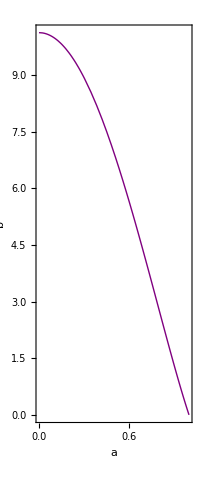

```mathematica
Separatrix=ParametricPlot[{acrp[λ],bcr[λ]},{λ,1,3/2},PlotRange->All,AspectRatio->Full,Frame->True,FrameLabel->{Style[" a ",Medium,Black],Style[" b ",Medium,Black],Style[" Separatrix (n = 4) ",Medium,Black]}, PlotStyle->{Purple, Thick}]
```

______________________________ o O o ______________________________
CRITICAL MANIFOLD

The Critical manifold is a surface spanned by all critical points ycr, in the  space {ycr,a,b,},  obtained as these parameters vary continuously. Critical ycr, solving for the event-horizon Ui=0: The solutions ycr: Yi, Yii, Yiii, Yiv, in eq.(26) results from:

```mathematica
rootsn4=Solve[Ui[y,a,b]==0,y];
```

```mathematica
yi=Level[rootsn4,{3}][[2]];
```

```mathematica
yii=Level[rootsn4,{3}][[4]];
```

```mathematica
yiii=Level[rootsn4,{3}][[6]];
```

```mathematica
yiv=Level[rootsn4,{3}][[8]];
```

Store the solutions, yi, yii, yiii and yiv:
Yi[ a_ ,  b_ ] := yi, Yii[ a_ ,  b_ ] := yii,  Yiii[ a_ ,  b_ ] := yiii, and Yiv[ a_ ,  b_ ] := yiv; 
and calculate the event-horizon surface:  manifoldi.

```mathematica
manifoldi=Plot3D[{yiv,yiii,yii,yi},{a,0,1},{b,0,12},PlotRange->All,TicksStyle-> Directive[Blue,12],AxesLabel->{"  a [m]", "b", "  r [m]"},AspectRatio->Full]
```

-Graphics3D-

Again, the Separatrix is obtained as a parametric curve on the parameter sub-space {a,b,0}:

```mathematica
separarixi=ParametricPlot3D[{acrp[λ],bcr[λ],0},{λ,1,1.5},PlotStyle->{Red,Thick},AspectRatio->Full]
```

-Graphics3D-

```mathematica
FIGURE 8:
```

```mathematica
Show[manifoldi,separarixi]
```

-Graphics3D-

```mathematica
Figure 8. Shown is the surface of allowed horizons for n=3 (left panel) and n=4 (right panel).Shown is also the projected curve of the separatrix.The vertical axis denotes r in units of m0,the x-axis
the a in units of m0 and the y-axis the bn=b parameter.The figures are obtained using (25).The
corresponding MATEMATICA[44] tool can be retrieved from[45].
```

______________________________ o O o ______________________________
CRITICAL PARAMETERS and CRITICAL VARIABLES COALESCENCE

Solve λ ,  for a(λ) = 0 and a(λ) = 1/2:

```mathematica
Solve[acrp[λ]==0,λ]
```

{{λ→0},{λ→3/2}}

We take λ = 3/2 ,  for a(λ) = 0:

```mathematica
{acrp[3/2],bcr[3/2]}
```

{0,81/8}

```mathematica
Solve[acrp[λ]==1/2,λ]
N[%]
```

{{λ→1/4 (3-√7)},{λ→1/4 (3+√7)}}

{{λ→0.0885622},{λ→1.41144}}

```mathematica
N[{acrp[1/4 (3+√7)],bcr[1/4 (3+√7)]}]
```

{0.5,6.9413}

______________________________ o O o ______________________________
CRITICAL LOCI  and  COALESCENCE

```mathematica
λ=1/4 (3+√7);
N[%]
N[{acrp[λ],bcr[λ]}]
Chop[N[U[Yiv[acrp[λ],bcr[λ]],acrp[λ],bcr[λ]]]]
pa1=Graphics[{Black,Circle[{bcr[λ],U[Yiv[acrp[λ],bcr[λ]],acrp[λ],bcr[λ]]},0.05]}];
λ=.
```

1.41144

{0.5,6.9413}

1.00315

```mathematica
λ=3/2;
N[{acrp[λ],bcr[λ]}]
{U[Yiv[acrp[λ],bcr[λ]],acrp[λ],bcr[λ]],Chop[N[U[Yiv[acrp[λ],bcr[λ]],acrp[λ],bcr[λ]]]]}
pa2=Graphics[{Black,Circle[{bcr[λ],U[Yiv[acrp[λ],bcr[λ]],acrp[λ],bcr[λ]]},0.05]}];
λ=.
```

{0.,10.125}

{243/160,1.51875}

```mathematica
______________________________ o O o ______________________________
CRITICAL U  and  COALESCENCE
```

1/4 (3+√7)

1.41144

{1/2,6.9413}

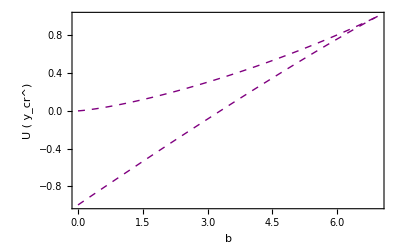

```mathematica
λ=1/4 (3+√7)
N[λ]
{1/2,N[bcr[λ]]}
Ucr1=Plot[{U[Yiv[1/2,b],1/2,b],U[Yiii[1/2,b],1/2,b]},{b,0,bcr[λ]},Frame->True,FrameLabel->{Style[" b ",Large,Black],Style[" U ( y_cr^) ",Large,Black]}, PlotStyle->{{Purple, Thick, Dashed},{Purple, Thick,Dashed}}, FrameLabel->Automatic]
λ=.
```

3/2

{0,81/8}

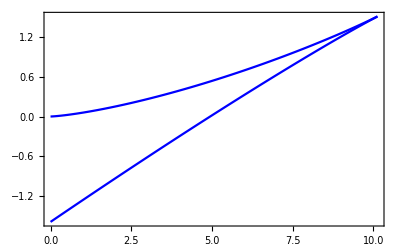

```mathematica
λ=3/2
{0,bcr[λ]}
Ucr2=Plot[{U[Yiv[0,b],0,b],U[Yiii[0,b],0,b]},{b,0,bcr[λ]},Frame->True, PlotStyle->{{Blue},{Blue}}]
λ=.
```

```mathematica
FIGURE 9:
```

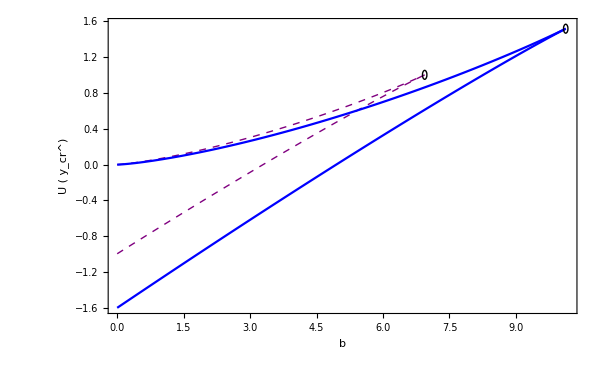

```mathematica
Show[Ucr1,Ucr2,pa1,pa2,PlotRange-> All,Frame->True]
```

Figure 9. Shown are two plots for n = 4, a = 0.5 m_0 (dashed), and a = 0 m_0 (continuous):   U (y_cr^iv(0.5,b),0.5,b), and  U (y_cr^iii(0,b),0,b), respectively (y=r/m_0 ). Each plot represents extrema  of U(y_cr), for a fixed  parameter a  and  as a function of  parameter b≡ b_n. In each of these plots, the  upper part corresponds to maxima and the lower one to minima. Each curve caoleses at its corresponding critical poin  within the Separatrix,  Eq.(32), and they are indicated as  small circles. Critical values were calculated from Eq.(25), from a Mathematica routine (available in [45]).

______________________________ o O o ______________________________
Stability Shapes vs. Parameter Space Regions (Figure 10)

2

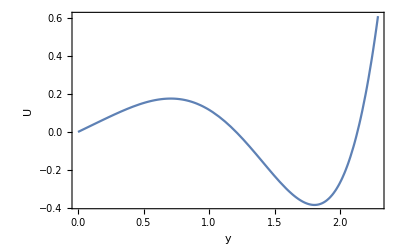

```mathematica
b=2
Ua=Plot[U[y,0.5,b],{y,0,2.29},PlotRange-> All,Frame->True,FrameLabel->{y,U,"b = 2" }]
b=.
```

3.3

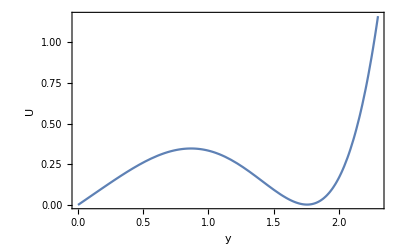

```mathematica
b=3.3
Ua=Plot[U[y,0.5,b],{y,0,2.3},PlotRange-> All,Frame->True,FrameLabel->{y,U,"b = 3.3" }]
b=.
```

```mathematica
FrameLabel->{"y","U","{acrp[1/4 (3+√7)] = 1/2 ,   b = bcr[1/4 (3+√7)]}" }
```

4

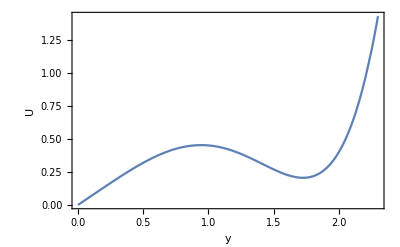

```mathematica
b=4
Ua=Plot[U[y,0.5,b],{y,0,2.3},PlotRange-> All,Frame->True,FrameLabel->{y,U,"b = 4" }]
b=.
```

```mathematica
N[bcr[1/4 (3+√7)]]
```

6.9413

```mathematica
N[acrp[1/4 (3+√7)]]
```

0.5

6.9413

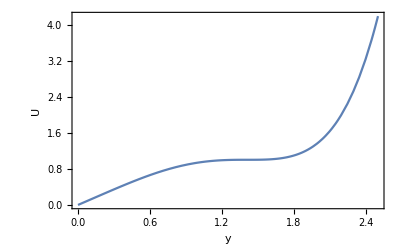

```mathematica
b=N[bcr[1/4 (3+√7)]]
Ua=Plot[U[y,0.5,b],{y,0,2.5},PlotRange-> All,Frame->True,FrameLabel->{"y","U","{acrp[1/4 (3+√7)] = 1/2 ,   b = bcr[1/4 (3+√7)]}" }]
b=.
```

10

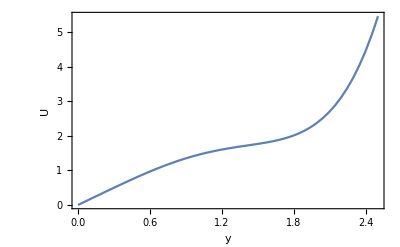

```mathematica
b=10
Ua=Plot[U[y,0.5,b],{y,0,2.5},PlotRange-> All,Frame->True,FrameLabel->{"y","U","{ a = 0.5 ,   b = 10 }" }]
b=.
```

______________________________ o O o ______________________________
Critical surfaces (manifolds) for the Event-Horizon, and Light-Ring Fig. (11).

The Light-Ring is obtained from eq.(38), giving:

```mathematica
V[y_,a_,b_]:=3(b-6 y^3)a y^2+2(b-3 y^3)a^3-2 √(a^2+b/(6 y^2)+y(y-2)) (3 y^6+a^2(b-3 y^3))+√(y-b/(3 y^2))(6 y^6+a^2(6 y^3(y+2)-b))
```

```mathematica
LiRia= ContourPlot3D[V[y,a,b]==0,{a,0.02,1},{b,0.01,10.125},{y,3/2,3},PlotPoints->30,Mesh ->False,ContourStyle->Directive[Yellow,Opacity[0.5],Specularity[White,10]],PlotRange->All]
```

-Graphics3D-

```mathematica
EventHorizontn4=ContourPlot3D[Ui[y,a,b]==0,{a,0.01,1},{b,0.01,10.125},{y,3/2,3},Axes->True,AxesStyle->{Directive[Black,15],Directive[Black,15],Directive[Blue,15]}, Mesh->{0,12},MeshStyle->{White,Yellow}, PlotPoints->40,PlotRange->All,AxesLabel->{Style[a,Large,Black],Style[b,Large,Black],Style[Subscript[y, cr],Large,Blue]},AspectRatio->Full,ContourStyle->Directive[Blue,Opacity[0.75],Specularity[White,30]]]
```

-Graphics3D-

```mathematica
Show[EventHorizontn4,LiRia,ViewPoint->Above]
```

-Graphics3D-